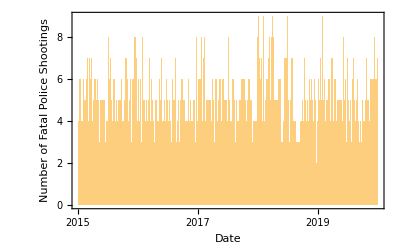

```mathematica
data:=Import["shootingdata.csv"][[2;;4939,3]]
DateHistogram[data,"Day",Ticks->{{"2015","2016","2017","2018","2019","2020"},Automatic},Frame->True,FrameLabel->{"Date","Number of Fatal Police Shootings"}]
```